# Complex Variables Toolkit - Final Project - Nathan Yee

## About

### This notebook serves as a group of utilities (functions) that allow a user to interact with and understand complex functions. In particular it provides functions that give exponential and sphere (inverse stereograph) based spacings, point based circle creation, point based line and grid creation, complex image map utilities, additional color creation tools, stereographic projection utilities, 3D printing tools and examples, and finally Newton’s method animation utilities. As an added benefit to the user, every function has a usage line (Mathematica equivalent of docstring), and at least one example of how it is used.

### The line below tells Mathematica to save all initialization cells to a .m file. This is the file that will be imported in the future whenever one wants to use the toolkit.

```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->Automatic]
```

## Functions

### Provided below are the functions, documentation, and examples.

## Exponential, and Sphere based Spacings

### Various types of spacings serve as the foundation for circle, line, and grid point generator functions.

### Inverse (default Log) spaced points

```mathematica
fSpace[min_,max_,numPts_,f_: Log]:=Module[{},N[InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(numPts-1)]]]
fSpace::usage="fSpace[min, max, steps, Log] gives inverse f (default Log) spaced points from min to max over a given number of points";
```

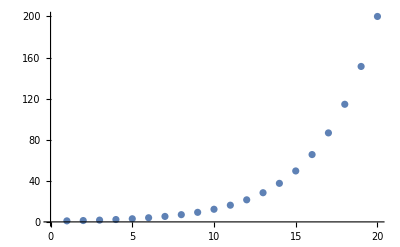

```mathematica
ListPlot[fSpace[1,200,20,Log]]
```

### Sphere spaced points

```mathematica
makeRiemannRealAxis[numPts_]:=Module[
{angles, pts},
angles=N@Range[0Pi,2Pi,(2 Pi - 0Pi)/(numPts - 1)];
pts=Table[{Cos[ang],0,Sin[ang]},{ang,angles}];
Return[pts]
]
makeRiemannRealAxis::usage="makeRiemannRealAxis[numPts_] makeRiemannRealAxis returns equally spaced points around the positive real axis on the Riemann Sphere";
```

```mathematica
realAxis3D=makeRiemannRealAxis[30];
ListPointPlot3D[realAxis3D,AspectRatio->1,PlotStyle->PointSize[.03],ImageSize->Large]
```

-Graphics3D-

```mathematica
riemannPointToComplexPlane[{X_,Y_,Z_}]:=Module[{sol,pair},
sol=Solve[{x+ⅈ y==(X+ⅈ Y)/(1-Z)},{x∈Reals,y∈Reals}];
pair=({x,y}/.sol)[[1]];
Return[pair]
]
riemannPointToComplexPlane::usage="riemannPointToComplexPlane[{X_,Y_,Z_}] 
riemannPointToComplexPlane returns the inverse stereographic projection of a point distance 1 from the origin in 3D space";
```

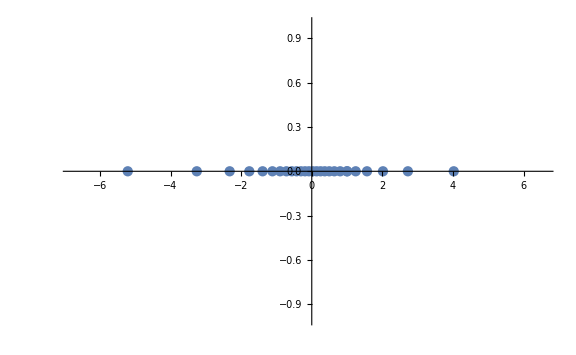

```mathematica
realAxis2D=riemannPointToComplexPlane[#]&/@realAxis3D;
ListPlot[realAxis2D,ImageSize->Large]
```

```mathematica
makeSphereSpacedPoints[numPts_]:=Module[{pts,complexPts,realPts},
pts=makeRiemannRealAxis[numPts];
complexPts=riemannPointToComplexPlane[#]&/@pts;
realPts=complexPts[[All,1]];
Return[realPts]
]
makeSphereSpacedPoints::usage="makeSphereSpacedPoints[numPts_] makeSphereSpacedPoints returns the inverse stereographic projection of points around the positive real axis on the Riemann Sphere. It gets the positive real axis of the Riemann Sphere by calling makeRiemannRealAxis. It finds the inverse stereographic projection of the points by mapping riemannPointToComplexPlane onto each point";
```

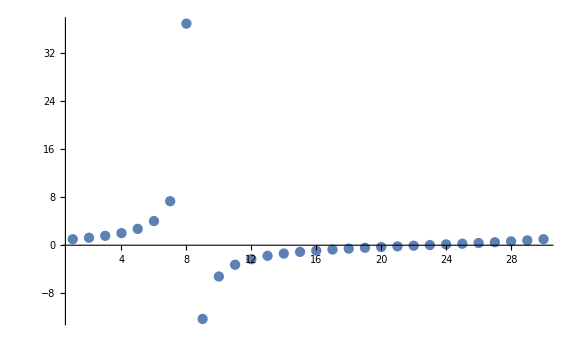

```mathematica
ListPlot[makeSphereSpacedPoints[30],PlotRange->All,ImageSize->Large]
```

## Circle Creation

### Point based circle generator functions are useful tool to visualize complex mappings.

### Linear spaced circles

```mathematica
makeCirclePoints[smallRadius_,largeRadius_,numCircles_,ptsPerCircle_]:=Module[{ang, lists, pts},
ang=Range[0 Pi,2 Pi,(2π-0)/(ptsPerCircle-1)];
lists=Table[{r Cos[ang],r Sin[ang]},{r,Range[smallRadius,largeRadius,(largeRadius-smallRadius)/(numCircles-1)]}];
pts=Transpose[#]&/@lists;
Return[pts]
]
makeCirclePoints::usage="makeCirclePoints[smallRadius_,largeRadius_,numCircles_,ptsPerCircle_] 
makeCirclePoints returns expanding circles given smallest radius, largest radius, step size, and number of points per circle. 
The constant step size dictates that the radius of the circles increases by a constant step size per circle";
```

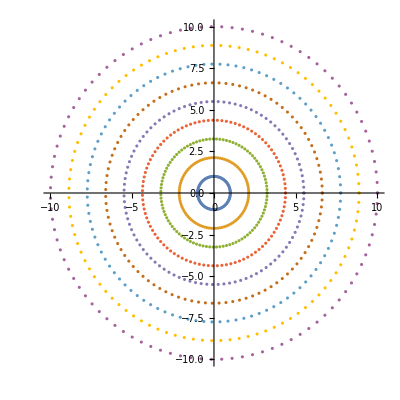

```mathematica
ListPlot[makeCirclePoints[1,10,9,100],AspectRatio->1]
```

### Exponentially spaced circles

```mathematica
makeExponentialSpacedCirclePoints[smallRadius_,largeRadius_,numCircles_,ptsPerCircle_]:=Module[{ang, lists, pts},
ang=Range[0 Pi,2 Pi,(2π-0)/(ptsPerCircle-1)];
lists=Table[{r Cos[ang],r Sin[ang]},{r,fSpace[smallRadius,largeRadius,numCircles]}];
pts=Transpose[#]&/@lists;
Return[pts]
]
makeExponentialSpacedCirclePoints::usage="makeExponentialSpacedCirclePoints[smallRadius_,largeRadius_,numCircles_,ptsPerCircle_] makeExponentialSpacedCirclePoints returns expanding circles given smallest radius, largest radius, number of circles, and number of points per circle. The number of circles dictates that the circles be spaced exponentially within the largestRadius - smallestRadius range";
```

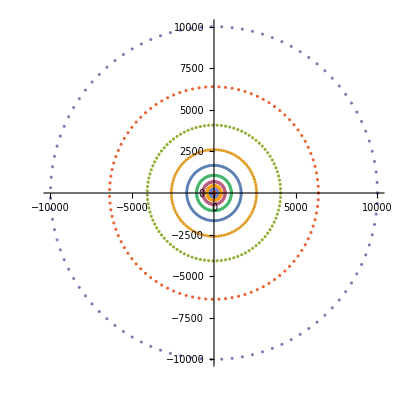

```mathematica
ListPlot[makeExponentialSpacedCirclePoints[2,10000,20,100],AspectRatio->1,PlotRange->Full]
```

### “Sphere” spaced circles

```mathematica
makeSphereSpacedCirclePoints[numCircles_,ptsPerCircle_]:=Module[{ang, lists, pts},
ang=Range[0 Pi,2 Pi,(2π-0)/(ptsPerCircle-1)];
lists=Table[{r Cos[ang],r Sin[ang]},{r,makeSphereSpacedPoints[numCircles]}];
pts=Transpose[#]&/@lists;
Return[pts]
]
makeSphereSpacedCirclePoints::usage="makeSphereSpacedCirclePoints[numCircles_,ptsPerCircle_] makeSphereSpacedCirclePoints returns circles based on inverse stereographic projection given a number of circles, and the number of points per circle";
```

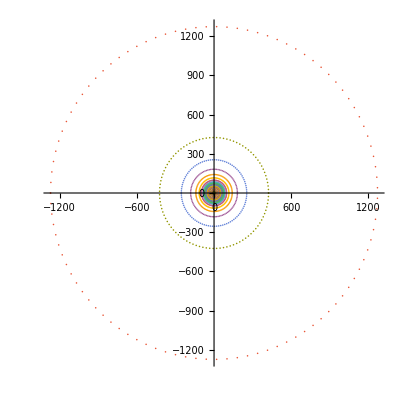

```mathematica
ListPlot[makeSphereSpacedCirclePoints[1000,100],AspectRatio->1,PlotRange->Full]
```

## Line and Grid creation

### Point based line and grid generator functions are useful tool to visualize complex mappings.

### Linearly spaced lines and grids

```mathematica
makeVerticalPts[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{y,Range[minY,maxY,(maxY-minY)/(ptsPerLine-1)]}],{x,minX,maxX,(maxX-minX)/(numLines-1)}];
Return[horiPts]
]
makeVerticalPts::usage="makeVerticalPts[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_] 
returns numLines number of vertical lines of equally spaced points starting from minX to maxX with length maxY-minY with ptsPerLine number of points per line";
```

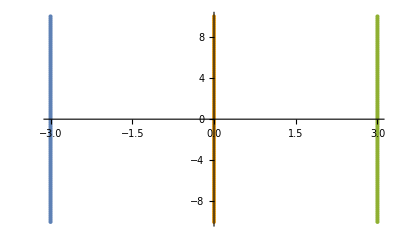

```mathematica
ListPlot[makeVerticalPts[-3,3,-10,10,100,3],PlotRange->Full]
```

```mathematica
makeHorizontalPts[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{x,Range[minX,maxX,(maxX-minX)/(ptsPerLine-1)]}],{y,minY,maxY,(maxY-minY)/(numLines-1)}];
Return[horiPts]
]
makeHorizontalPts::usage="makeHorizontalPts[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_] 
returns numLines number of horizontal lines of equally spaced points starting from minY to maxY with length maxX-minX with ptsPerLine number of points per line";
```

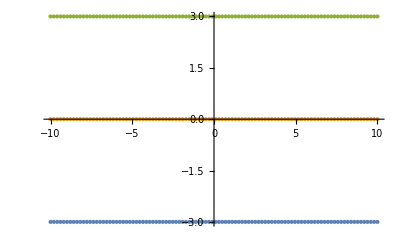

```mathematica
ListPlot[makeHorizontalPts[-10,10,-3,3,100,3],PlotRange->Full]
```

```mathematica
makeGridPts[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_]:=Module[{vertPts,horiPts,pts},
vertPts=makeVerticalPts[minY,maxY,minX,maxX,ptsPerLine,numLines];
horiPts=makeHorizontalPts[minX,maxX,minY,maxY,ptsPerLine,numLines];
pts=Join[horiPts,vertPts];
Return[pts]
]
makeGridPts::usage="makeGridPts[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_] 
returns numLines number of vertical of equally spaced points lines starting from minX to maxX with 
length maxY-minY with ptsPerLine number of points per line and 
returns numLines number of horizontal of equally spaced points lines starting from minY to maxY with 
length maxX-minX with ptsPerLine number of points per line.
NOTE: enter args as if doing horizontal line";
```

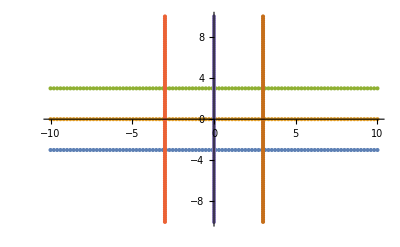

```mathematica
ListPlot[makeGridPts[-10,10,-3,3,100,3],PlotRange->Full]
```

### Exponentially spaced lines and grids

```mathematica
makeLogVerticalPts2[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_]:=Module[{vertPts},
vertPts=Table[Table[{x,y},{y,fSpace[minY,maxY,ptsPerLine]}],{x,minX,maxX,(maxX-minX)/(numLines-1)}];
Return[Re[vertPts]]
]
makeLogVerticalPts2::usage="makeLogVerticalPts2[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_] 
returns numLines number of vertical lines of exponentially spaced points starting from minX to maxX with length maxY-minY with ptsPerLine number of points per line.
NOTE: makeLogVerticalPts2 is depreciated due to not handling negative minY to positive maxY ranges";
```

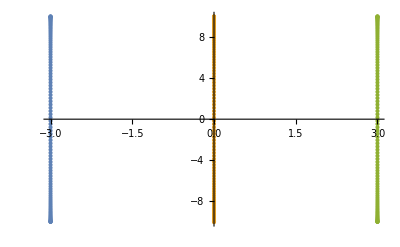

```mathematica
ListPlot[makeLogVerticalPts2[-3,3,-10,10,100,3],PlotRange->Full]
```

```mathematica
makeLogHorizontalPts2[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{x,fSpace[minX,maxX,ptsPerLine]}],{y,minY,maxY,(maxY-minY)/(numLines-1)}];
Return[Re[horiPts]]
]
makeLogHorizontalPts2::usage="makeLogHorizontalPts2[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_] 
returns numLines number of horizontal lines of exponentially spaced points starting from minY to maxY with 
length maxX-minX with ptsPerLine number of points per line
NOTE: makeLogHorizontalPts2 is depreciated due to not handling negative minX to positive maxX ranges";
```

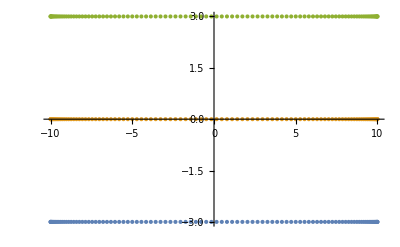

```mathematica
ListPlot[makeLogHorizontalPts2[-10,10,-3,3,100,3],PlotRange->Full]
```

```mathematica
makeLogVerticalPts[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_]:=Module[
{posVertPts,negVertPts,pts},
posVertPts=Table[Table[{x,y},{y,fSpace[.01,maxY,Floor[ptsPerLine/2]]}],{x,minX,maxX,(maxX-minX)/(numLines-1)}];
negVertPts=Table[Table[{x,y},{y,fSpace[minY,-.01,Floor[ptsPerLine/2]]}],{x,minX,maxX,(maxX-minX)/(numLines-1)}];
pts=MapThread[Join,{negVertPts,posVertPts}];
Return[Re[pts]]
]
makeLogVerticalPts::usage="makeLogVerticalPts[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_] 
returns numLines number of vertical lines of exponentially spaced points starting from minX to maxX with length maxY-minY with ptsPerLine number of points per line.";
```

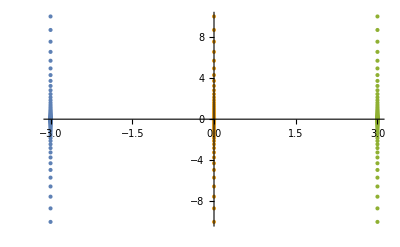

```mathematica
ListPlot[makeLogVerticalPts[-3,3,-10,10,100,3],PlotRange->Full]
```

```mathematica
makeLogHorizontalPts[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_]:=Module[
{posHoriPts,negHoriPts,pts},
posHoriPts=Table[Table[{x,y},{x,fSpace[.01,maxX,Floor[ptsPerLine/2]]}],{y,minY,maxY,(maxY-minY)/(numLines-1)}];
negHoriPts=Table[Table[{x,y},{x,fSpace[minX,-.01,Floor[ptsPerLine/2]]}],{y,minY,maxY,(maxY-minY)/(numLines-1)}];
pts=MapThread[Join,{negHoriPts,posHoriPts}];
Return[Re[pts]]
]
makeLogHorizontalPts::usage="makeLogHorizontalPts[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_] 
returns numLines number of horizontal lines of exponentially spaced points starting from minY to maxY with length maxX-minX with ptsPerLine number of points per line";
```

```mathematica
ListPlot[makeLogHorizontalPts2[-10,10,-3,3,100,3],PlotRange->Full]
```

-Graphics-

```mathematica
makeLogGridPts[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_]:=Module[
{vertLogPts,horiLogPts,pts},
vertLogPts=makeLogVerticalPts[minY,maxY,minX,maxX,ptsPerLine,numLines];
horiLogPts=makeLogHorizontalPts[minX,maxX,minY,maxY,ptsPerLine,numLines];
pts=Join[horiLogPts,vertLogPts];
Return[pts]
]
makeLogGridPts::usage="makeLogGridPts[minX_,maxX_,minY_,maxY_,ptsPerLine_,numLines_] 
returns numLines number of vertical of exponentially spaced points lines starting from minX to maxX 
with length maxY-minY with ptsPerLine number of points per line and 
returns numLines number of horizontal of exponentially spaced points lines starting from minY to maxY 
with length maxX-minX with ptsPerLine number of points per line.
NOTE: enter args as if doing horizontal line";
```

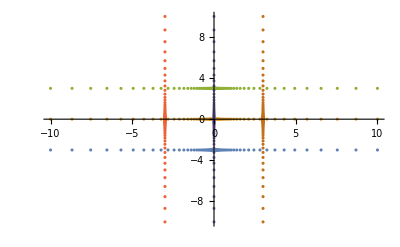

```mathematica
ListPlot[makeLogGridPts[-10,10,-3,3,100,3],PlotRange->Full]
```

### Sphere spaced lines and grids

```mathematica
makeSphereVerticalLines[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts,spherePts},
spherePts=makeSphereSpacedPoints[ptsPerLine];
horiPts=Table[Table[{x,y},{y,spherePts}],{x,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]
makeSphereVerticalLines::usage=
	"makeSphereVerticalLines[min_,max_,ptsPerLine_,numLines_] makes vertical lines of 
	sphere spaced points given line bounds of min, max, ptsPerLine, and numLines";
```

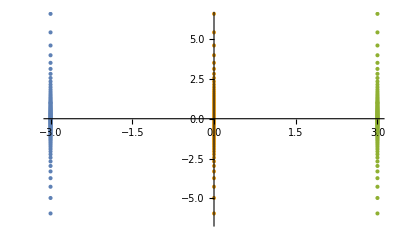

```mathematica
ListPlot[makeSphereVerticalLines[-3,3,100,3]]
```

```mathematica
makeSphereHorizontalLines[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts,spherePts},
spherePts=makeSphereSpacedPoints[ptsPerLine];
horiPts=Table[Table[{x,y},{x,spherePts}],{y,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]
makeSphereHorizontalLines::usage="makeSphereHorizontalLines[min_,max_,ptsPerLine_,numLines_] makes horizontal lines of sphere spaced points given line bounds of min, max, ptsPerLine, and numLines";
```

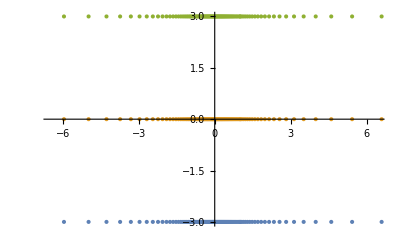

```mathematica
ListPlot[makeSphereHorizontalLines[-3,3,100,3]]
```

```mathematica
makeSphereGrid[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts,horiPts,pts},
vertPts=makeSphereVerticalLines[min,max,ptsPerLine,numLines];
horiPts=makeSphereHorizontalLines[min,max,ptsPerLine,numLines];
pts=Join[horiPts,vertPts];
Return[pts]
]
makeSphereGrid::usage="makeSphereGrid[min,max,ptsPerLine,numLines] makes a grid of sphere spaced points given line bounds of min, max, ptsPerLine, and numLines";
```

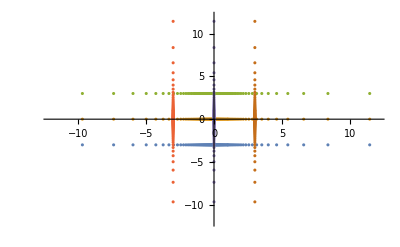

```mathematica
ListPlot[makeSphereGrid[-3,3,100,3]]
```

## Complex Plane to Image Plane

### Here we make functions that let us deal with lists of points on the complex plane, a mapping expression, and the resulting image plane.

### Get image of points

```mathematica
getImagePts[expr_,pts_]:=Module[{imgPts},
imgPts={Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}&/@#&/@pts;
Return[imgPts]]
getImagePts::usage="getImagePts[expr[z],pts] returns the image points given takes in an expression of z and a list of lists of lists of points";
```

```mathematica
getImagePts[z+1-ⅈ,{{{1,1},{2,2}}}]
```

{{{2,0},{3,1}}}

### Plot image of points

```mathematica
plotImage[pts_,expr_,pltRange1_: Automatic,PltRange2_: Automatic,colors_: 1]:=Module[{},
If[colors==1,colors=RGBColor[1,1,1],colors=colors];
{
Graphics[MapThread[{#1,Thick,Line[#2]}&,{colors,pts}],PlotRange->pltRange1,Axes->True,Background->White,ImageSize->{300,300},AxesLabel->{Style["x",Italic],Style["y",Italic]},ImagePadding->20],Graphics[MapThread[{#1,Thick,Line[{Re[expr/.z->#[[1]]+I #[[2]]],Im[expr/.z->#[[1]]+I #[[2]]]}&/@#2]}&,{colors,pts}],PlotRange->PltRange2,Axes->True,Background->White,ImageSize->{300,300},AxesLabel->{Style["u",Italic],Style["v",Italic]},ImagePadding->20]
}
]
plotImage::usage="plotImage[pts,expr,pltRange1:Automatic,PltRange2:Automatic,colors:1] returns a list containing the complex and image plots given a list of lists of lists of points, an expression of z, two plot ranges (can be Automatic), and a list of colors. Note that plotImage doesn't call getImagePts so we can MapThread with color gradients";
```

{RGBColor[0.5, 0.1, 0.7],RGBColor[0.5, 0.3666666666666667, 0.7],RGBColor[0.5, 0.6333333333333333, 0.7],RGBColor[0.5, 0.9, 0.7]}

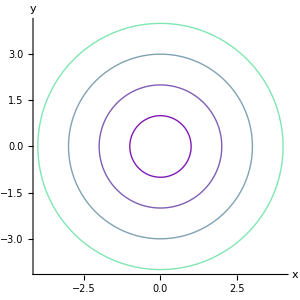
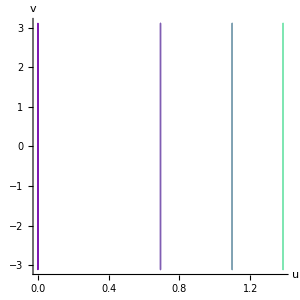
Complex Plane | ImagePlane
-Graphics- | -Graphics-

```mathematica
circles=Quiet[makeCirclePoints[1,4,4,100]];
circleColors=makeColorGradient[circles]
Quiet@Grid[{{"Complex Plane","ImagePlane"},plotImage[circles,Log[z],Automatic,Automatic,circleColors]}]//TraditionalForm
```

## Colors

### Color functions further help the user understand what is going on in complex plane to image plane or Riemann Sphere mappings.

```mathematica
makeRandomColors[pts_]:=Module[{colors},
colors=RandomColor[Length[pts]];
Return[colors]]
makeRandomColors::usage="makeRandomColors[pts_] returns length of pts number of random RBG colors";
```

```mathematica
makeRandomColors[{{0,0},{1,1},{2,2},{3,3},{4,4}}]
```

{RGBColor[0.42771769833613393, 0.36056033305481683, 0.8746870615193874],RGBColor[0.8244329078065329, 0.13679213335179186, 0.07836791003021881],RGBColor[0.6610505382406149, 0.9090339224934629, 0.006138480351362663],RGBColor[0.26063650571133, 0.4623797097842799, 0.7080302571685475],RGBColor[0.8888782237976469, 0.30740458064678333, 0.4987662941520534]}

```mathematica
makeColorGradient[pts_]:=Module[{colors},
colors=Table[RGBColor[.5,x,.7],{x,.1,.9,(.9-.1)/(Length[pts]-1)}];
Return[colors]]
makeColorGradient::usage="makeColorGradient[pts_] returns length of pts number of colors in a purple -> teal gradient";
```

```mathematica
makeColorGradient[{{0,0},{1,1},{2,2},{3,3},{4,4}}]
```

{RGBColor[0.5, 0.1, 0.7],RGBColor[0.5, 0.30000000000000004, 0.7],RGBColor[0.5, 0.5, 0.7],RGBColor[0.5, 0.7000000000000001, 0.7],RGBColor[0.5, 0.9, 0.7]}

## Riemann Sphere Stereographic Projection

### Here we make functions that allow the the projection of points on the complex plane to the Riemann Sphere through the use of stereographic projection

### Single point

```mathematica
complexTo3D[point_]:=Module[{x,y,z,mix,X,Y,Z},
x=point[[1]];
y=point[[2]];
mix=(2x+ⅈ 2y)/(1+x^2+y^2);
X=Re[mix];
Y=Im[mix];
z=x+ⅈ y;
Z=(Abs[z]^2-1)/(Abs[z]^2+1);
Return[{X,Y,Z}]
]
complexTo3D::usage="complexTo3D[point_] returns the stereographic projection of a point on the complex plane";
```

```mathematica
complexTo3D[{1,1}]
```

{2/3,2/3,1/3}

### Multiple points

```mathematica
complexPtsTo3D[points_]:=Module[{spherePts3D},
spherePts3D=complexTo3D[#]&/@#&/@points;
Return[spherePts3D]
]
complexPtsTo3D::usage="complexPtsTo3D[points_] returns the stereographic projection of a list
of points on the complex plane";
```

```mathematica
gridPts2D=makeSphereGrid[-3,3,100,3];
gridPts3D=complexPtsTo3D[gridPts2D];
ListPointPlot3D[gridPts3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

### Color Graphics3D test

```mathematica
colors3D=makeColorGradient[gridPts3D]
Graphics3D[MapThread[{#1,Thick,Line[#2]}&,{colors3D,gridPts3D}],AspectRatio->1,ImageSize->Large]
```

{RGBColor[0.5, 0.1, 0.7],RGBColor[0.5, 0.26, 0.7],RGBColor[0.5, 0.42000000000000004, 0.7],RGBColor[0.5, 0.5800000000000001, 0.7],RGBColor[0.5, 0.7400000000000001, 0.7],RGBColor[0.5, 0.9000000000000001, 0.7]}

-Graphics3D-

## 3D printing

### 3D printing allows us to take what we see in the computer and hold it in real life.

### Connecting cylinders

```mathematica
takingPts[takes_,pts_]:=Module[{newPts},
newPts=Take[pts,#]&/@takes;
Return[newPts]]
takingPts::usage="takingPts[takes_,pts_] returns a list of taken points 
given a list of takes and a list of points";
```

```mathematica
takingPts[{{1,2},{2,3},{3,4}},{2,7,4,0}]
```

{{2,7},{7,4},{4,0}}

```mathematica
cylinderPts[pts_]:=Module[{takes},
takes=Table[{x,x+1},{x,1,Dimensions[pts][[2]]-1}];
Return[takingPts[takes,#]&/@pts]
]
cylinderPts::usage="cylinderPts[pts_] returns a list of taken points ready to be converted to cylinders";
```

```mathematica
cylinderPts[{{{1,2,3},{4,5,6},{7,8,9},{10,11,12}}}]
```

{{{{1,2,3},{4,5,6}},{{4,5,6},{7,8,9}},{{7,8,9},{10,11,12}}}}

```mathematica
cylinders[pts_,radius_]:=Module[{},
Return[Cylinder[#,radius]&/@#&/@cylinderPts[pts]]]
cylinders::usage="cylinders[pts_,radius_] returns cylinders linearly along the path of the list of points with specified radius";
```

```mathematica
Graphics3D[cylinders[{{{1,2,3},{2,2,3},{2,3,3},{3,3,3}}},.05]]
```

-Graphics3D-

### Connecting tubes

```mathematica
tubes[pts_,radius_]:=Module[{},Tube[#,radius]&/@complexPtsTo3D[pts]]
tubes::usage="tubes[pts_,radius_] returns tubes linearly
 along the path of the list of points with specified radius. This is
sometimes used as it gives a better result than cylinders but is less
reliable";
```

```mathematica
Graphics3D[tubes[{{{1,2,3},{2,2,3},{2,3,3},{3,3,3}}},.05]]
```

-Graphics3D-

### Exporting stls

```mathematica
gridPts2D=makeSphereGrid[-3,3,100,3];
gridPts3D=complexPtsTo3D[gridPts2D];
```

```mathematica
Export["grid2.stl",Graphics3D[cylinders[gridPts3D,.05]],{"STL,","BinaryFormat"->True}]
```

grid2.stl

```mathematica
Import["grid2.stl"]
```

-Graphics3D-

```mathematica
Export["grid_10_7.stl",Graphics3D[cylinders[complexPtsTo3D[makeSphereGrid[-1,1,100,12]],.01]],{"STL,","BinaryFormat"->True}]
```

grid_10_7.stl

```mathematica
grid107=Import["grid_10_7.stl"]
```

-Graphics3D-

## Newtons Method

### Newton’s Method illustrates how visualizations of complex mappings helps us understand numerical methods.

```mathematica
makeNewtonMethodAnimation[plotRange_,map_,depth_,points_]:=Module[{localPts,plots},
localPts=points;
plots=Flatten[{
{ListPlot[localPts,PlotRange->{{-plotRange,plotRange}, {-plotRange,plotRange}},PlotStyle->PointSize[.02],AspectRatio->1,ImageSize->Large]},
Table[
(*Apply map to grid pts*) localPts=getImagePts[map,localPts];
ListPlot[localPts,PlotRange->{{-plotRange,plotRange}, {-plotRange,plotRange}},PlotStyle->PointSize[.02],AspectRatio->1,ImageSize->Large]
,{n,1,depth}]
}];
Return[Manipulate[plots[[n]],{n,1,Length[plots],1}]]]
makeNewtonMethodAnimation::usage="makeNewtonMethodAnimation[plotRange,map,depth,points] makes animation of successive mappings";
```

```mathematica
f[z_]:=z^3-1
```

Use definition of Newton’s Method to derive mapping function

```mathematica
map=(z-f[z]/f'[z]);
```

Make a circular grid:

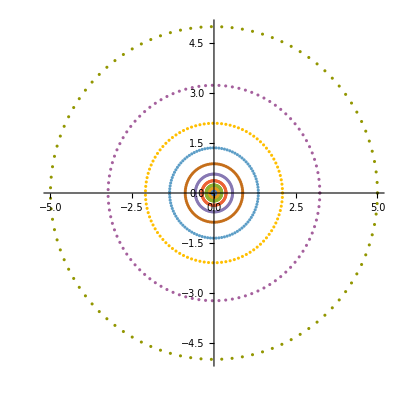

```mathematica
smallestRadius=.1;
largestRadius=5;
numberOfCircles=10;
pointsPerCircle=100;
circleGrid = makeExponentialSpacedCirclePoints[smallestRadius,largestRadius,numberOfCircles,pointsPerCircle];
circleGridCopy1=circleGrid;
ListPlot[circleGridCopy1,AspectRatio->1,PlotRange->Full]
```

```mathematica
makeNewtonMethodAnimation[5,map,35,circleGrid]
```